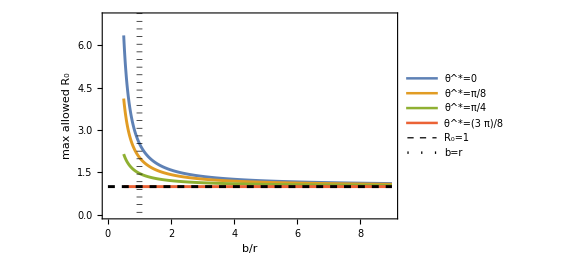
-Graphics-(B)

```mathematica
maxR0plotfns2 = Table[Exp[Cos[t]/boverr],{t,π/8,π/2,π/8}];
maxR0plot2=Plot[Evaluate@maxR0plotfns2,{boverr,0.5,9},
Frame->{True,True,False,False},
FrameLabel->{"b/r","max allowed R_0"},
FrameStyle->Directive[{Black}],
PlotRange->{0,7},
PlotLegends->{"θ^*=0",HoldForm[SuperStar[θ]=π/8],HoldForm[SuperStar[θ]=π/4],HoldForm[SuperStar[θ]=(3π)/8],HoldForm[SuperStar[θ]=π/2]} ,

 Ticks->Automatic,
AxesStyle->Directive[Black,Thick],
TicksStyle->Directive[FontSize->24,Black],
LabelStyle->{Directive[FontSize->24,Black]},
PlotStyle->{Thickness[0.005]}];
exR0plots2=Plot[1,{boverr,0,9},
(*PlotRange->{0,9},*)
PlotLegends->{"R_0=1"}, 
(*ScalingFunctions->{Automatic,"Log"}(*,"Log"}*),*)
PlotStyle->{Dashed,Black,Thickness[0.005]},
LabelStyle->Directive[FontSize->24,Black]];
bequalsrline = Legended[
Show[ 
Graphics[{Dotted,Black,Thickness[0.01],Line[{{1,-1},{1,8}}]}]
],LineLegend[{Directive[{Dotted,Black,Thickness[.01]}]},{"b=r"},LabelStyle->Directive[FontSize->24,Black]]];
(*immgaplines2 =
Legended[
Show[ 
Graphics[{Dashed,Blue,Thickness[0.005],Line[{{5,-1},{5,8}}]}]
],LineLegend[{Directive[{Dashed,Blue,Thickness[0.005]}]},{"blind spot threshold"},LabelStyle->Directive[FontSize->24,Black]]];*)
r0boundsplot=Show[maxR0plot2,exR0plots2, bequalsrline,(*immgaplines2,*)ImageSize->420];(*,immgaplines2]*)
r0boundsfig = Labeled[r0boundsplot,{Style["(B)",24,Black]},{{Top, Left}}]
```

## R0 Bounds fig

```mathematica
r0bounddensityplot = 
Show[DensityPlot[UnitStep[E^(1/x)-R0],{x,0,5.3},{R0,0,10.4},
PlotPoints->10, 
AxesStyle->Black,
BaselinePosition->Axis,AxesOrigin->{0,5.175},
FrameLabel->{{Style[HoldForm["R_0"],24,Black],None},{Style["b/(r cos SuperscriptBox[θ, *])",24,Black],Style["sometext",24,White]}},
ColorFunction->Function[y,ColorData["BrightBands"][0.3*(y)]],
FrameTicksStyle->Directive[FontSize->24,Black]
 ],ImageSize->450];
```

```mathematica
r0boundfiga = Show[r0bounddensityplot, Graphics[Text[Style["Allowed",24],{1.5,0.8}]],Graphics[Text[Style["Forbidden",24],{3,8}]],ImageSize->270];
r0boundfig = Show[Labeled[r0boundfiga,{Style["(A)",24,Black]},{{Top, Left}}]];


r0boundcombined=GraphicsRow[{r0boundfig,r0boundsfig},ImageSize->1000]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Export["../figures/r0_bound.pdf",r0boundcombined]
```

../figures/r0_bound.pdf